```mathematica
ClearAll["Global`*"];
NotebookDirectory[];
SetDirectory[NotebookDirectory[]]; (* or else the default directory is Directory[]*)
NotebookDirectory[];
```

# Active SSH

### Parameters

```mathematica
Mms=6.7*^-4; (*0.5*)
Rms=0.26*0.2;(*0.09*)
Cmc=2.13*^-4;(*1/0.42*)
omega0 = 1/Sqrt[Mms*Cmc];


sd=12*^-4;(* m^2 diaphragm surface *)
S=0.05*0.05; (*  m^2 duct cross section*)
rho0=1.184;(*[kg/m^3]*)
c0=346;(*%[m/s]*)
a=0.2806;(*[m]*)
kk =1*(-sd)+  0*1/Cmc; (*Coupling negative*)

zs[k_] := (ⅈ  k c0)*Mms + Rms + 1/( (ⅈ  k c0)*Cmc);
zr:= rho0 c0 sd/S;
```

### Speaker mechanical impedance

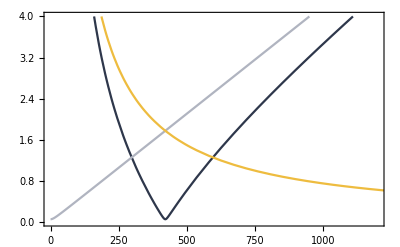

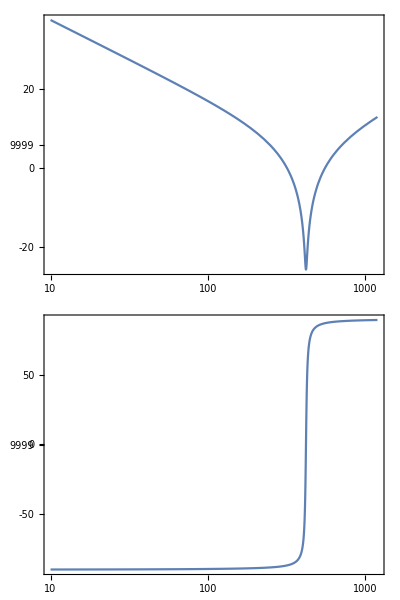

```mathematica
Zms[freq_]:= (I*2*Pi*freq)*Mms + Rms + 1/((I*2*Pi*freq)*Cmc);
ZmsAbv[freq_]:= (I*2*Pi*freq)*Mms + Rms ;
ZmsBlw[freq_]:=  Rms + 1/((I*2*Pi*freq)*Cmc);

Plot[{Abs[Zms[freq] ] ,Abs[ZmsAbv[freq]] ,Abs[ZmsBlw[freq] ]},{freq,0.1,2200},PlotRange->{{0,1200},{0,4}},PlotStyle->{ColorData["GrayYellowTones",0],ColorData["GrayYellowTones",0.5],ColorData["GrayYellowTones",1]},Frame->True]
BodePlot[Zms[f],{f,10,1200}]
```

### Transfer Matrix

```mathematica
(*
z11[k_] := zs[k]+kk/(ⅈ c0 k);
z12[k_] := -kk/(ⅈ c0 k);
z21[k_] :=z12[k];
z22[k_] :=z11[k];
zMat[k_]:=  ({{z11[k], z12[k]}, {z21[k], z22[k]}});
yMat[k_]:=Inverse[zMat[k]];
y11[k_]:= Part[yMat[k],1,1];
y12[k_]:= Part[yMat[k],1,2];
y21[k_]:= Part[yMat[k],2,1];
y22[k_]:= Part[yMat[k],2,2];
*)
T1[k_] := ({{Exp[-I k a/4], 0}, {0, Exp[+I k a/4]}});

T2[k_] :=({{((-1+ⅇ^(ⅈ a k)) (kk-sd) (kk+sd) zr^2+4 zs[k] (ⅇ^((ⅈ a k)/2) kk zr-sd zr+zs[k]))/(2 zs[k] ((-1+ⅇ^(ⅈ a k)) kk zr+2 ⅇ^((ⅈ a k)/2) zs[k])), (zr ((kk-sd) (kk+sd) zr Sin[(a k)/2]-2 ⅈ (kk-sd Cos[(a k)/2]) zs[k]))/(2 (kk zr Sin[(a k)/2]-ⅈ zs[k]) zs[k])}, {(zr ((-kk^2+sd^2) zr Sin[(a k)/2]+2 ⅈ (kk-sd Cos[(a k)/2]) zs[k]))/(2 (kk zr Sin[(a k)/2]-ⅈ zs[k]) zs[k]), -((-1+ⅇ^(ⅈ a k)) (kk-sd) (kk+sd) zr^2+4 ⅇ^((ⅈ a k)/2) kk zr zs[k]-4 ⅇ^(ⅈ a k) zs[k] (sd zr+zs[k]))/(2 zs[k] ((-1+ⅇ^(ⅈ a k)) kk zr+2 ⅇ^((ⅈ a k)/2) zs[k]))}});

Ttot[k_]= T1[k].T2[k].T1[k];
```

```mathematica
M11[k_]:= Part[Ttot[k],1,1];
M12[k_]:= Part[Ttot[k],1,2];
M21[k_]:= Part[Ttot[k],2,1];
M22[k_]:= Part[Ttot[k],2,2];
M[k_]:= {{M11[k],M12[k]},{M21[k],M22[k]}} ;
```

### Scattering Matrix

```mathematica
SS[k_]:= {{-M21[k]/M22[k],1/M22[k]},{M11[k]-M12[k]*M21[k]/M22[k],M12[k]/M22[k]}};

(*MatrixForm[SS[k]]//FullSimplify*)


ReImPlot[SS[2*Pi*freq/c0],{freq,0.1,1200},PlotRange->{{0,1200},{0,1}},Frame->True];
```

### Dispersion

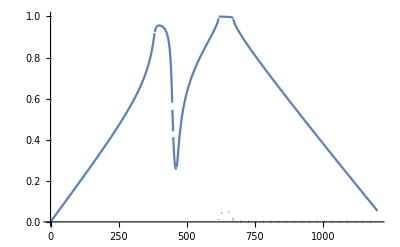

```mathematica
TrFunc[k_]:= Tr[M[k]]/2 ;
(*TrFunc[k_]:= Tr[M[k]]- Sqrt[Tr[M[k]]^2-4*Det[Tr[M[k]]]];*)
(*TraceM1[k_]:= (M11[k]+ M22[k])/2- Sqrt[((M11[k]+ M22[k])/2)^2+M12[k]+ M21[k]];*)

q[k_] :=ArcCos[ TrFunc[k]]/a;
q[k]//FullSimplify;
FullSimplify[%];
(*ToMatlab[%];*)
ReImPlot[q[2*Pi*freq/c0]*a/Pi,{freq,0.1,1200},PlotRange->{{0,1200},{0,1}}]
```

### Energy conserving = S-matrix is unitary

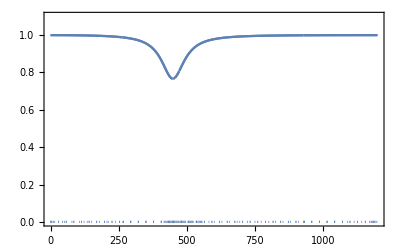

```mathematica
ReImPlot[SS[2*Pi*freq/c0].Transpose[Conjugate[SS[2*Pi*freq/c0]]],{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]
```

### SU (1, 1) group?

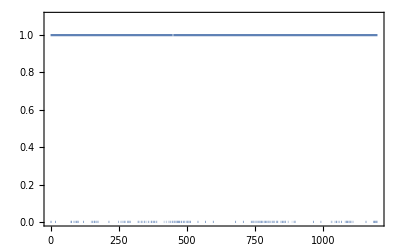

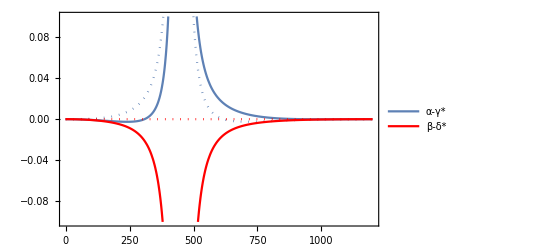

```mathematica
ReImPlot[M11[2*Pi*freq/c0]*M22[2*Pi*freq/c0] - M12[2*Pi*freq/c0]*M21[2*Pi*freq/c0] ,{freq,0.1,1200},PlotRange->{{0,1200},{0,1.1}},Frame->True]


alphaGamma[freq_]:= M11[2*Pi*freq/c0]-Conjugate[M22[2*Pi*freq/c0]];
meanAlphaGamma := Mean[alphaGamma[Range[0.1,1200,0.1]]];
stdAlphaGamma:= StandardDeviation[alphaGamma[Range[0.1,1200,1]]];

betaDelta[freq_]:= M12[2*Pi*freq/c0]-Conjugate[M21[2*Pi*freq/c0]];
meanBetaDelta := Mean[betaDelta[Range[0.1,1200,1]]];
stdBetaDelta:= StandardDeviation[betaDelta[Range[0.1,1200,1]]];


p1 = ReImPlot[(alphaGamma[freq]- 0*meanAlphaGamma)/stdAlphaGamma ,{freq,0.1,1200},PlotRange->{{0,1200},{-0.1,0.1}},Frame->True,PlotLegends->LineLegend[{"α-γ*"}]];
p2 = ReImPlot[(betaDelta[freq]- 0*meanBetaDelta)/stdBetaDelta ,{freq,0.1,1200},PlotRange->{{0,1200},{-0.1,0.1}},Frame->True,PlotLegends->LineLegend[{"β-δ*"}],PlotStyle->Red];
Show[p1,p2, PlotRange->All]

(*ReImPlot[MatrixPower[M[2*Pi*freq/c0],2],{freq,0.1,1200},PlotRange->{{0,1200},{-2,2}},Frame->True]*)
```

### Topology

```mathematica
AlphaR[k_]:= Re[M11[k]]
AlphaI[k_]:=Im[M11[k]]
BetaR[k_]:=Re[M21[k]]
BetaI[k_]:=Im[M21[k]]

coneplot = Plot3D[{Sqrt[x^2+y^2],-Sqrt[x^2+y^2]},{x,-2,2},{y,-2,2},
RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic,
ColorFunction->"RustTones",
PlotStyle->Opacity[0.5],
Mesh-> False,
Boxed->False,
Axes->False,
AxesOrigin->{0,0,0},
AxesStyle->Opacity[1],
TicksStyle->None,
AxesLabel->{Style[hi,16],Style[y,16],Style[z,16]},
ViewPoint->{Pi,Pi/2,2},Background->None]
(*Export["cone.png",coneplot,Background->None,ImageResolution-> 300]*)

Directory[]
```

-Graphics3D-

\\files7.epfl.ch\data\padlewsk\My Documents\PhD\acoustic-projects-master\active-dimer\simulation\mathematica\AA3